## RegularPolygon-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51e (11 June 2017)) loaded Tue 13 Jun 2017 15:18:02
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

```mathematica
p=regularPolygon[7]
```

{{1.,0.},{0.62349,0.781831},{-0.222521,0.974928},{-0.900969,0.433884},{-0.900969,-0.433884},{-0.222521,-0.974928},{0.62349,-0.781831}}

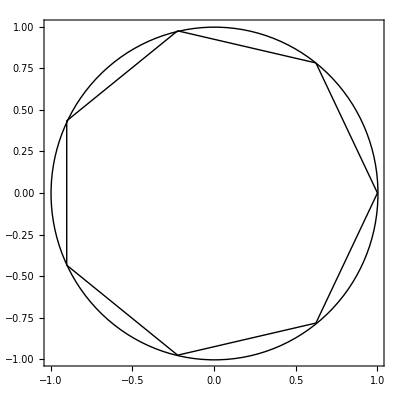

```mathematica
Show[Boundary[p],Graphics[Circle[{0,0}, 1]],  Frame-> True]
```

```mathematica
q=regularPolygon[7, Pi/2, 2, -1, 3Pi/4]
```

{{1.41421,-1.41421},{1.43459,-0.328909},{0.374686,1.00407},{-0.96736,1.58096},{-1.58096,0.96736},{-1.00407,-0.374686},{0.328909,-1.43459}}

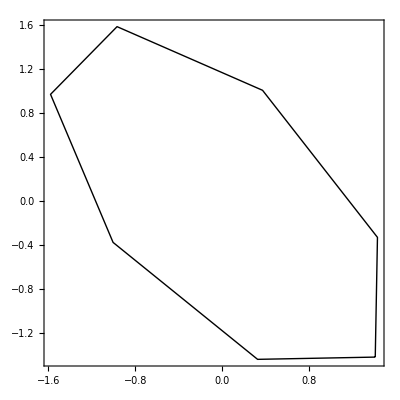

```mathematica
Show[Boundary[q], Frame-> True]
```

```mathematica
r=regularPolygon[7, Pi/2, 2, .5, 3Pi/4]
```

{{1.49611,-1.37206},{1.30957,-0.504633},{0.194,1.51553},{-1.02594,1.48579},{-1.19756,0.944306},{-1.24822,-0.638274},{0.389704,-1.89873}}

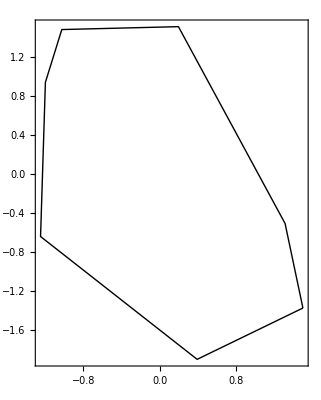

```mathematica
Show[Boundary[r], Frame-> True]
```